```mathematica
CloseKernels[];
LaunchKernels[16];
```

### Definitions

#### Real 16

```mathematica
DecToReal16[x_]:=Module[{m,e,s,sign,exponent,fraction,data},
sign={1-UnitStep[x]};
If[x==0||x==-0,
exponent={0,0,0,0,0};
fraction={0,0,0,0,0,0,0,0,0,0};
,
{m,e}=N[MantissaExponent[x,2]];
m =Abs[m];

If[e+14<1,
exponent={0,0,0,0,0};
fraction=RealDigits[m*2^(e+14-1),2,11,-1][[1,2;;]];
,
exponent=First@RealDigits[e+14,2,5,4];
fraction=RealDigits[m,2,11,-1][[1,2;;]];
];
];
data = Join[sign,exponent,fraction];
Join[data[[9;;]],data[[;;8]]]
];
Real16ToDec[bin_]:=Module[{sign,exponent,fraction={0,0,0,0,0,0,0,0,0,0,0},val},
sign=bin[[1]];
exponent=bin[[2;;6]];
fraction=Join[{0},bin[[7;;]]];
val = 0;
If[exponent=={0,0,0,0,0},
fraction[[1]]=0;
val=(-1)^sign * 2^(-14)*FromDigits[{fraction,1},2];
,
If[exponent=={1,1,1,1,1},
If[fraction == {0,0,0,0,0,0,0,0,0,0,0},
If[sign==0,
val = Infinity,
val = -Infinity
];
,
val = Indeterminate;
];
,
fraction[[1]]=1;
val =(-1)^sign * 2^(FromDigits[exponent,2]-15)*FromDigits[{fraction,1},2];
];
];
N[val]
];

Clear[MyExport];
Clear[MyImport];
MyExport[file_,data_,{"Binary","Real16"}]:=Export[file,Flatten[DecToReal16/@data],"Bit"];
MyExport[file_,data_,format_]:=Export[file,data,format];
MyImport[file_,{"Binary","Real16"}]:=Map[Real16ToDec,Partition[Import[file,"Bit"],16]];
MyImport[file_,format_]:=Import[file,format];
```

#### Tests

```mathematica
val = 5 ;
bin=DecToReal16[val]
N[val]
res = Real16ToDec[bin]
Abs[(val-res)/val]
```

{0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0}

5.

5.

0.

```mathematica
ParallelTable[Max[(#-Real16ToDec[DecToReal16[#]])/#&/@RandomReal[{2^-16,2^i},{10000}]],{i,-10,16}]
ParallelTable[Max[(#-Real16ToDec[DecToReal16[#]])/#&/@RandomReal[{-2^-16,-2^i},{10000}]],{i,-10,16}]
```

{0.00294098,0.00338101,0.00318952,0.0034505,0.00341794,0.00301404,0.00261809,0.00204461,0.00184295,0.00107705,0.000955794,0.00096395,0.000968161,0.000972673,0.000967059,0.000966062,0.00097034,0.000959817,0.00096585,0.000973741,0.000965623,0.000953943,0.000953224,0.00096441,0.000960262,0.000971635,0.000961168}

{0.00330202,0.00349116,0.00265176,0.00320208,0.00271622,0.00179146,0.00178021,0.001677,0.00104253,0.000956451,0.000949566,0.000957342,0.00095512,0.000958594,0.000963555,0.000962387,0.000963605,0.000959527,0.000968747,0.000966379,0.000966048,0.000968091,0.000963659,0.000964787,0.000970493,0.000967976,0.000955454}

```mathematica
MyExport[FileNameJoin[{path,"test.raw16"}],{1,2,3,4},{"Binary","Real16"}]
MyImport[FileNameJoin[{path,"test.raw16"}],{"Binary","Real16"}]

MyExport[FileNameJoin[{path,"test.raw32"}],{1,2,3,4},{"Binary","Real32"}]
MyImport[FileNameJoin[{path,"test.raw32"}],{"Binary","Real32"}]
```

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/test.raw16

{1.,2.,3.,4.}

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/test.raw32

{1.,2.,3.,4.}

#### Test data

```mathematica
path=FileNameJoin[{NotebookDirectory[],"datasets"}];

formats={
{"UINT8","UnsignedInteger8",0,2^8-1},
{"UINT12","UnsignedInteger16",0,2^12-1},
{"UINT16","UnsignedInteger16",0,2^16-1},
{"UINT32","UnsignedInteger32",0,2^32-1},
{"UINT64","UnsignedInteger64",0,2^64-1},(* Not in opengl*)
{"INT8","Integer8",-2^7,2^7-1},
{"INT12","Integer16",-2^11,2^11-1},
{"INT16","Integer16",-2^15,2^15-1},
{"INT32","Integer32",-2^31,2^31-1},
{"INT64","Integer64",-2^63,2^63-1}, (* Not in opengl *)
{"FLOAT16","Real16",0,1},(* Are store on disk as Real32, only use "16 in gpu" .. not any more...*)
{"FLOAT32","Real32",0,1},
{"FLOAT64","Real64",0,1} (* Not in opengl *)
};

ClearAll[f,g,makeTestData,writeTestData,writeVecTestData];
f[{i_,j_,k_},{x_,y_,z_},{w_,h_,d_}]:=Boole[x<=i<x+w&&y≤j<y+h&&z≤k<z+d];

g[{i_,j_,k_},{min_,max_}]:=
min + 
(*Diag*)
Sum[
(max-min)*(k/100)*f[{i,j,k},{s,s,s},{10,10,10}],
{s,1,100,10}] + 
(*Corners*)
(max-min)*(i/100)*f[{i,j,k},{11,1,1},{90,10,10}]+
(max-min)*(j/100)*f[{i,j,k},{1,11,1},{10,90,10}]+
(max-min)*(k/100)*f[{i,j,k},{1,1,11},{10,10,90}]+
(max-min)*(i/100)*f[{i,j,k},{80,80,1},{20,20,20}]+
(max-min)*(k/100)*f[{i,j,k},{80,1,80},{20,20,20}]+
(max-min)*(j/100)*f[{i,j,k},{1,80,80},{20,20,20}];

makeTestData[{min_,max_}]:=ParallelTable[
g[{i,j,k},{min,max}],
{i,1,100},{j,1,100},{k,1,100}];

writeTestData[path_,filename_,data_,format_,binformat_,range_]:=Module[{datdata,fun=Identity},
datdata = "Rawfile: <file>
Resolution: <dim>
Format: <format>
BasisVector1: 1.0 0.0 0.0
BasisVector2: 0.0 1.0 0.0
BasisVector3: 0.0 0.0 1.0
DataRange: <datarange>
ValueRange: 0 1
ValueUnit: arb. unit";

If[StringMatchQ[format,___~~"INT"~~___],fun =Floor];

Print@MyExport[FileNameJoin[{path,filename<>".raw"}],fun[Flatten[data]],{"Binary",binformat}];
Print@Export[FileNameJoin[{path,filename<>".dat"}],StringReplace[datdata,{
"<file>"->filename<>".raw",
"<dim>"->StringJoin[Riffle[ToString/@Dimensions[data]," "]],
"<format>" ->format,
"<datarange>" ->StringJoin[Riffle[ToString/@range," "]]}],"String"];
];

writeVecTestData[path_,filename_,data_,format_,binformat_,range_,vec_]:=Module[{datdata,fun=Identity,localdata},
datdata = "Rawfile: <file>
Resolution: <dim>
Format: <format>
BasisVector1: 1.0 0.0 0.0
BasisVector2: 0.0 1.0 0.0
BasisVector3: 0.0 0.0 1.0
DataRange: <datarange>
ValueRange: 0 1
ValueUnit: arb. unit";

If[StringMatchQ[format,___~~"INT"~~___],fun =Floor];

localdata =Flatten[Transpose[Table[fun[Flatten[data]],{vec}]]];

Print@MyExport[FileNameJoin[{path,filename<>".raw"}],localdata,{"Binary",binformat}];
Print@Export[FileNameJoin[{path,filename<>".dat"}],StringReplace[datdata,{
"<file>"->filename<>".raw",
"<dim>"->StringJoin[Riffle[ToString/@Dimensions[data]," "]],
"<format>" ->If[vec>1,"Vec"<>ToString[vec],""]<>format,
"<datarange>" ->StringJoin[Riffle[ToString/@range," "]]}],"String"];
];
```

```mathematica
makeTestForRange[name_, formats_,ranges_]:=Module[{format,range,test},
Assert[Length[formats]==Length[ranges]];
Do[
format=formats[[i]];
range=ranges[[i]];
Print["Name: ",name," Format: ",format," Range: ",range];
test = makeTestData[range];
Do[
writeVecTestData[path,"testdata."<>name<>"."<>If[vec>1,"Vec"<>ToString[vec],""]<>format[[1]]<>"",test,format[[1]],format[[2]],range,vec];
,{vec,1,4}];
,{i,1,Length[formats]}
];
];
```

### Debug

```mathematica
test = makeTestData[{0,255}];
Image3D[test]
```

-Graphics3D-

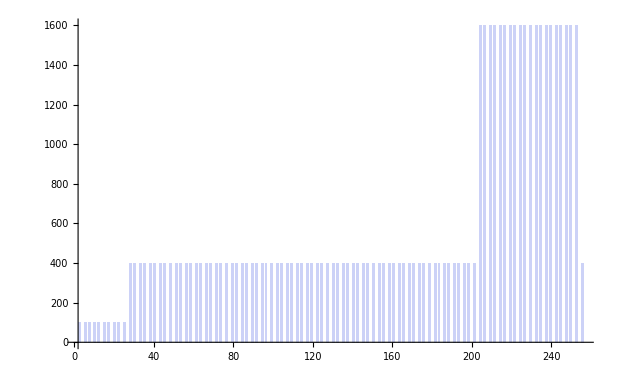

```mathematica
Histogram[Cases[Flatten[test],x_/;x≠0],{1}]
```

## Test data

```mathematica
On[Assert];
```

```mathematica
sets = {};
```

### Generate test data over the whole data range

```mathematica
newRanges = Table[ {format[[3]],format[[4]]},{format,formats}];
AppendTo[sets,{"defaultRange",newRanges}];
```

### Generate test data over [0, random max]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"INT"~~___],
{0,RandomInteger[{1,format[[4]]}]}
,
{0,RandomReal[{0,10000}]}
],{format,formats}]
```

```mathematica
newRanges={{0,95},{0,2836},{0,16189},{0,2027728223},{0,4443979578008950143},{0,76},{0,1192},{0,30200},{0,1772200050},{0,3781332457807923215},{0,9246.589872024415},{0,9636.743062168542},{0,5756.798134971106}};
AppendTo[sets,{"zeroToMax",newRanges}];
```

### Generate test data over [random min > 0, random max]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"INT"~~___],
 Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{0,format[[4]]}],{2}]]
,
Sort[RandomReal[{0,10000},{2}]]
],{format,formats}]
```

```mathematica
newRanges ={{116,211},{60,1913},{3443,39306},{676169744,2470222196},{12941944102923495242,13951824418797592805},{31,59},{1329,1944},{4712,31446},{1777417123,1920490697},{7858752822474560636,8834913215675668326},{552.627975796564,1980.1671998594375},{7680.661781476381,9911.748881093506},{3758.2397317603263,7113.834991256725}};
AppendTo[sets,{"posMinToMax",newRanges}];
```

### Generate test data over [random min < 0 (0 for unsigned), random max]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"INT"~~___],
 Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{format[[3]],format[[4]]}],{2}]]
,
{RandomReal[{-10000,0}],RandomReal[{0,10000}]}
],{format,formats}]
```

```mathematica
newRanges ={{12,74},{2633,3576},{9468,63774},{1462220780,3109666504},{5034554744896981213,15169865492495921882},{-12,123},{-483,2011},{19468,32531},{-207981349,2097493422},{-8512604166325398617,-8347961268893637350},{-6770.304994868615,4712.381426221171},{-8796.697931880013,4569.175049171639},{-4584.474233552743,8078.207564193388}};
AppendTo[sets,{"negMinToMax",newRanges}];
```

### Generate test data over [random min < 0 (0 for unsigned), random max < 0 (>0 for unsigned)]

```mathematica
newRanges = Table[
If[StringMatchQ[format[[1]],___~~"UINT"~~___],
 Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{format[[3]],format[[4]]}],{2}]]
,
If[StringMatchQ[format[[1]],___~~"INT"~~___],
Sort[RandomInteger[Clip[{format[[3]],format[[4]]},{format[[3]],0}],{2}]]
,
Sort[RandomReal[{-10000,0},{2}]]
]
],{format,formats}]
```

```mathematica
newRanges ={{32,116},{1236,1381},{4567,63404},{1613792279,1650415309},{6507014441663072600,16594246101605872729},{-98,-3},{-1267,-446},{-15560,-14400},{-1876666169,-316510283},{-5546276063223236586,-3222873741793228398},{-7497.1494100799955,-5261.78994786451},{-5399.083752463612,-1731.1421948878597},{-4043.298137163869,-45.78688351105302}};
AppendTo[sets,{"negMinToNegMax",newRanges}];
```

## Generate Data

```mathematica
sets={{"defaultRange",{{0,255},{0,4095},{0,65535},{0,4294967295},{0,18446744073709551615},{-128,127},{-2048,2047},{-32768,32767},{-2147483648,2147483647},{-9223372036854775808,9223372036854775807},{0,1},{0,1},{0,1}}},{"zeroToMax",{{0,95},{0,2836},{0,16189},{0,2027728223},{0,4443979578008950143},{0,76},{0,1192},{0,30200},{0,1772200050},{0,3781332457807923215},{0,9246.589872024415},{0,9636.743062168542},{0,5756.798134971106}}},{"posMinToMax",{{116,211},{60,1913},{3443,39306},{676169744,2470222196},{12941944102923495242,13951824418797592805},{31,59},{1329,1944},{4712,31446},{1777417123,1920490697},{7858752822474560636,8834913215675668326},{552.627975796564,1980.1671998594375},{7680.661781476381,9911.748881093506},{3758.2397317603263,7113.834991256725}}},{"negMinToMax",{{12,74},{2633,3576},{9468,63774},{1462220780,3109666504},{5034554744896981213,15169865492495921882},{-12,123},{-483,2011},{19468,32531},{-207981349,2097493422},{-8512604166325398617,-8347961268893637350},{-6770.304994868615,4712.381426221171},{-8796.697931880013,4569.175049171639},{-4584.474233552743,8078.207564193388}}},{"negMinToNegMax",{{32,116},{1236,1381},{4567,63404},{1613792279,1650415309},{6507014441663072600,16594246101605872729},{-98,-3},{-1267,-446},{-15560,-14400},{-1876666169,-316510283},{-5546276063223236586,-3222873741793228398},{-7497.1494100799955,-5261.78994786451},{-5399.083752463612,-1731.1421948878597},{-4043.298137163869,-45.78688351105302}}}};
```

```mathematica
inds={11};
makeTestForRange[#[[1]],formats[[inds]],#[[2]][[inds]]]&/@sets;
```

Name: defaultRange Format: {FLOAT16,Real16,0,1} Range: {0,1}

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.Vec2FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.Vec2FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.Vec3FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.Vec3FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.Vec4FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.defaultRange.Vec4FLOAT16.dat

Name: zeroToMax Format: {FLOAT16,Real16,0,1} Range: {0,9246.59}

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.Vec2FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.Vec2FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.Vec3FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.Vec3FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.Vec4FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.zeroToMax.Vec4FLOAT16.dat

Name: posMinToMax Format: {FLOAT16,Real16,0,1} Range: {552.628,1980.17}

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.Vec2FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.Vec2FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.Vec3FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.Vec3FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.Vec4FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.posMinToMax.Vec4FLOAT16.dat

Name: negMinToMax Format: {FLOAT16,Real16,0,1} Range: {-6770.3,4712.38}

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.Vec2FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.Vec2FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.Vec3FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.Vec3FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.Vec4FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToMax.Vec4FLOAT16.dat

Name: negMinToNegMax Format: {FLOAT16,Real16,0,1} Range: {-7497.15,-5261.79}

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.Vec2FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.Vec2FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.Vec3FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.Vec3FLOAT16.dat

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.Vec4FLOAT16.raw

/Users/petst/Work/Projects/Elstruct-vis/Inviwo/data/tests/datarangetest/datasets/testdata.negMinToNegMax.Vec4FLOAT16.dat